## Capítulo 2: Iteración

## 2.1. Iteración en la recta

Con el comando NestList podemos iterar sucesivamente una función:

```mathematica
NestList[f,a,5]
```

```mathematica
f[z_]=z^2;
NestList[f,0.9,10]
```

{0.9,0.81,0.6561,0.430467,0.185302,0.0343368,0.00117902,1.39008×10^-6,1.93233×10^-12,3.73392×10^-24,1.39421×10^-47}

Observe la convergencia a 1.

```mathematica
h[x_]=4x(1-x);
NestList[h,0.3,20]
```

El anterior es un caso de comportamiento caótico

### 2.1.3. El juego del caos

```mathematica
vertices = N[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]
```

```mathematica
inicio = Table[Random[],{2}]
```

```mathematica
verticeazar:=vertices[[RandomInteger[{1,3}]]]
```

```mathematica
siguiente[punto_] := (verticeazar + punto)/2
```

```mathematica
T[n_]:=ListPlot[NestList[siguiente, inicio, n],PlotRange->{{0,1},{0,Sqrt[3]/2}},AspectRatio->Sqrt[3]/2,Axes->False,PlotStyle->PointSize[0.011]]
```

```mathematica
Show[GraphicsGrid[{{T[10], T[50], T[100]},{T[200], T[500], T[1000]}, {T[5000], T[20000], T[50000]}}]]
```

## 2.3. Iteradas

A partir de ahora nos movemos en el plano complejo, entendiendo este como una división de una región del plano en un número elevado, pero finito de píxeles.

```mathematica
ListPlot[Flatten[Table[{x,y},{y,-1,1,.1},{x,-1.5,1.5,.1}],1]]
```

La iteración sucesiva también funciona con números complejos:

```mathematica
f[z_]:=(z)^2
NestList[f,z,6]
```

```mathematica
N[NestList[f,0.9+0.3 I,6]]
```

Podemos representar gráficamente las órbitas:

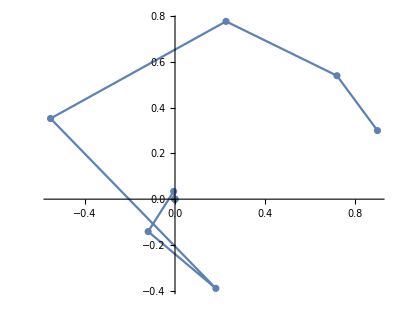

```mathematica
f[z_] := z^2;
x0=0.9+0.3I;
ComplexListPlot[N[FixedPointList[f,x0,10]]];
ComplexListPlot[N[FixedPointList[f,x0,10]],Joined->True];
Show[%,%%]
```

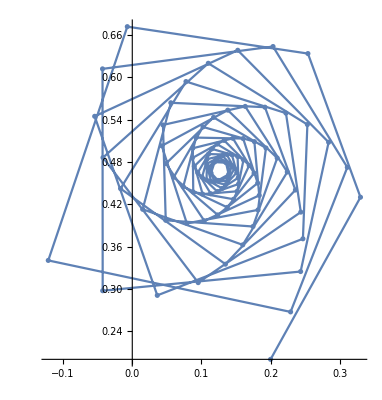

```mathematica
f[z_] := z^2+0.33+0.35I;
x0=0.2+0.2I;
(*ListPlot[{Re[#], Im[#]} & /@ FixedPointList[f, x0], PlotJoined -> True, AxesOrigin->{0,0}];*)
ComplexListPlot[FixedPointList[f, x0,100], AxesOrigin->{0,0.2}];
ComplexListPlot[FixedPointList[f, x0,100], Joined->True, AxesOrigin->{0,0.2}];
Show[%,%%]
```

```mathematica
f[z_] = z/2 + 1/z;
FixedPointList[f, 0.75 + 0.1I, SameTest->(Abs[#1-#2]<10^-4&)]
FixedPoint[f, 0.75 + 0.1I]
```

{0.75+0.1 ⅈ,1.68504-0.124672 ⅈ,1.43275-0.0186668 ⅈ,1.41421-0.000241452 ⅈ,1.41421-2.45537×10^-10 ⅈ,1.41421+3.57849×10^-18 ⅈ}

1.41421+0. ⅈ

## 2.4. Método de Newton

Definimos la función N_f(x) del método de Newton:

```mathematica
Clear[f,x] (* Eliminamos los posibles valores de f y x *)
iteracionN = #2-#1[#2]/Derivative[1][#1][#2] &;
iteracionN[f,x]
```

Para el caso x^2-1:

```mathematica
f[x_]:= x^2-1
iteracionN[f,x]
```

La raíz cuadrada de 2:

```mathematica
f = #^2-2&;
NestList[iteracionN[f,#] &, 2.0, 10]
```

### 2.4.1. Método de Newton en los complejos

La función de iteración es la misma

```mathematica
iteracionN = #2-#1[#2]/Derivative[1][#1][#2] &;
```

Definimos funciones que obtienen el argumento del valor al que converge la sucesión y la velocidad de convergencia:

```mathematica
newtonArgumento = Compile[{{z, _Complex}}, Arg[FixedPoint[iteracionN[f,#] &, z, 50]]];
newtonVelocidad = Compile[{{z,_Complex}}, Length[FixedPointList[iteracionN[f,#]&,z,50]]];
```

Con tan solo ajustar la función f y cambiar a nuestro gusto los parámetros se obtienen los gráficos.

```mathematica
f=#^3-1&;
GraphicsGrid[{{
DensityPlot[newtonArgumento[x+I*y], {x,-2,2}, {y,-2,2}, PlotPoints->300, Mesh->False, ColorFunction->"Rainbow", Frame->False],
DensityPlot[newtonVelocidad[x+I*y], {x,-2,2}, {y,-2,2}, PlotPoints->300, Mesh->False, ColorFunction->GrayLevel, Frame->False]}}]
```

```mathematica
f=#^6-1&; 
DensityPlot[newtonArgumento[x+I*y], {x,-2,2}, {y,-2,2}, PlotPoints->300, Mesh->False, ColorFunction->"Rainbow", Frame->False]
```

```mathematica
f=#^3-3^#&;
DensityPlot[newtonVelocidad[x+I*y], {x,-1,1.5}, {y,-1,1}, PlotPoints->300, Mesh->False, ColorFunction->"AvocadoColors", AspectRatio->Automatic,Frame->False]
```

```mathematica
f=#^2-2^#-1&;
DensityPlot[newtonVelocidad[x+I*y], {x,0.4, 0.6}, {y,-0.2,0.2}, PlotPoints->300, Mesh->False, ColorFunction->"NeonColors", AspectRatio->Automatic, Frame->False]
```

```mathematica
f=#^5-#^3+#^2-4&;
DensityPlot[newtonArgumento[x+I*y], {x,-1.5, 1.5}, {y,-1.5,1.5}, PlotPoints->300, Mesh->False, ColorFunction->"Rainbow", AspectRatio->Automatic, Frame->False]
```